w+w^2

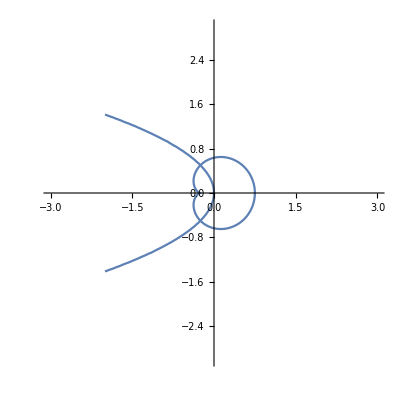

```mathematica
z=(x+I y);
r=.5;
phi[w_]=w+w^2
phii[w_]=1/2  *(-1+Sqrt[1+4 w]);
p1=ParametricPlot[{Re[phi[r Exp[I t]]],Im[phi[r Exp[I t]]]},{t,0,2 Pi},PlotRange->{{-3,3},{-3,3}}];
p2=ContourPlot[Abs[(phii[z]-.5)/(phii[z]+.5)]==1.0,{x,-2,2},{y,-2,2}];
Show[p1,p2]
```

-0.0442971-0.499204 ⅈ

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{w→-((0.153846+0.307692 ⅈ) ((-4.+16. ⅈ)+10. a-(2.+1. ⅈ) √((-165.+48. ⅈ)+(80.+480. ⅈ) a+400. a^2)))/((1.+6. ⅈ)+10. a)},{w→-((0.153846+0.307692 ⅈ) ((-4.+16. ⅈ)+10. a+(2.+1. ⅈ) √((-165.+48. ⅈ)+(80.+480. ⅈ) a+400. a^2)))/((1.+6. ⅈ)+10. a)}}

1.25571

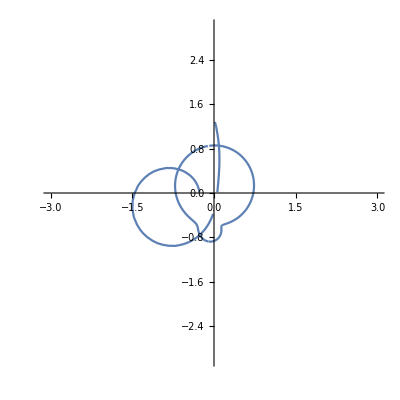

```mathematica
z=(x+I y);
c=.1+.2 I;
r=.65;
k = Sqrt[3]/2 + I/2;
phi[w_]=1/2(1/((w*r+c)+1/(w*r+c)) - 1.2I -0.2);
phi[0]
Solve[phi[w]- a == 0, w]


phii[a_]=-((0.15384615384615385+0.3076923076923077I) ((-1+2I)+a-(2+1 I) √(-1+4 a^2)))/a;
Abs[(phii[1I] - .5)/(phii[1I] + .5)]
p1=ParametricPlot[{Re[phi[ Exp[I t]]],Im[phi[ Exp[I t]]]},{t,0,2 Pi},PlotRange->{{-3,3},{-3,3}}];
p2=ContourPlot[Abs[(phii[z]-.5)/(phii[z]+.5)]==1.2,{x,-2,2},{y,-2,2}];
Show[p1,p2]
```

```mathematica
"
```